```mathematica
(* Filename: Errors_vs_Time_By_w1_SLE_tuck_A1_2A1_sym_DN
*)
(* Ver. 0 (28-Aug-2025) *)
(*
This file is a program code in Mathematica to get a plot about errors in Fig. 2.
*)
(*
Note that the following files should be excuted before this program:
a) Errors_By_w1_SLE_tuck_A1_2A1_sym_DN,
    b) Time_By_w1_SLE_tuck_A1_2A1_sym_DN.
*)
```

```mathematica
fdim=2;(* 2 *)
```

```mathematica
difflistMomAndTimeCForAve=Table[{},{ii,1,fdim}];
tmpMini=Table[{},{ii,1,5}];
For[ii=1, ii≤fdim, ii++,
tmpMini[[1]]={Log[2,timeC4Ave],Log[2,errorMomC4Ave[[ii]]]};
tmpMini[[2]]={Log[2,timeC8Ave],Log[2,errorMomC8Ave[[ii]]]};
tmpMini[[3]]={Log[2,timeC16Ave],Log[2,errorMomC16Ave[[ii]]]};
tmpMini[[4]]={Log[2,timeC32Ave],Log[2,errorMomC32Ave[[ii]]]};
tmpMini[[5]]={Log[2,timeC64Ave],Log[2,errorMomC64Ave[[ii]]]};
difflistMomAndTimeCForAve[[ii]]=Table[tmpMini[[ii]],{ii,1,5}];
];
```

```mathematica
plotlistMomAndTimeCForAve=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
plotlistMomAndTimeCForAve[[ii]]=ListPlot[difflistMomAndTimeCForAve[[ii]],PlotMarkers->{Graphics[{EdgeForm[{Thickness[0.1],Green}],Opacity[0],Polygon[{{0.5,0},{1,0.5},{0.5,1},{0,0.5}}]}],Scaled[0.045]}];
];
```

numSubSetForData=8

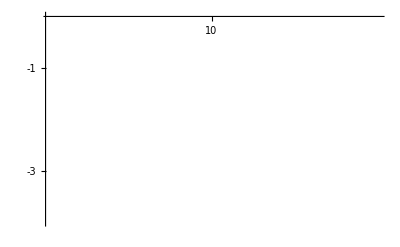

```mathematica
ll=0.03;
Print["numSubSetForData=",numSubSetForData];
ii=1;
Show[plotlistMomAndTimeCForAve[[ii]],PlotRange->{{8+0.06,12},{-4,0}},AxesOrigin->{8,0},Ticks->{Table[{1ii,ToString[1ii],ll},{ii,2,20}],Table[{-1ii,ToString[-1ii],ll},{ii,-3,8}]},BaseStyle->{14,FontFamily->"Helvetica"}]
```